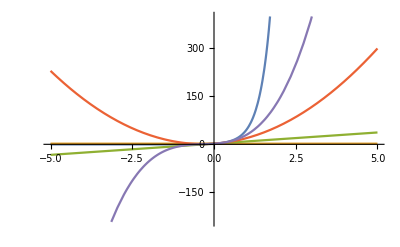

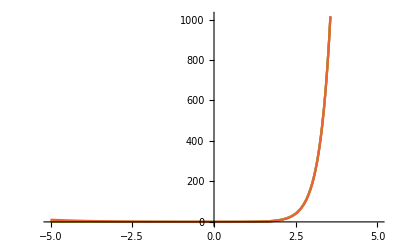

```mathematica
sol=y[x]/.DSolve[{y'[x]==3 y[x] +1 , y[0]==2},y[x],x];
svil[n_]:=Normal[Series[sol,{x,0,n}]]
Plot[Evaluate[{sol,Table[svil[j],{j,0,3}]}],{x,-5,5}]

Plot[Evaluate[Table[Abs[svil[j]-sol]/100,{j,0,3}]],{x,-5,5}]
```

```mathematica
(*-----------------------------*)
```

```mathematica
(*pc={y'[x_]==f[x_,y_],y[x0]==y0};*)
phi[0,x0]:=y0;
x0=0;
y0=2;
phi[n_,x_]:= y0 + Integrate[ f[t,phi[n-1,t]],{t,x0,x}]

f[x_,y_[a___]]=3 y[x] +1;

phi[2,5]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ∫_x0^t f[t,phi[-1020-1,t]]ⅆt.

Hold[y0+∫_x0^5 f[t,phi[2-1,t]]ⅆt]

```mathematica
(*----------*)
```

```mathematica
s1= x^2 +2 x y +y^2 ;
s2= lambda - 3 x^2 -6y^2 ;
lambda=5;
Plot3D[{s1,s2},{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
s1= x^2 +2 x y +y^2 ;
s2= lambda - 3 x^2 -6y^2 ;
solsist=lambda/.Solve[s1==s2,lambda]
Solve[solsist==0,y]
```

{4 x^2+2 x y+7 y^2}

{{y→-1/7 ⅈ (-ⅈ x+3 √3 x)},{y→1/7 ⅈ (ⅈ x+3 √3 x)}}

```mathematica
(*-------------------------*)
```